```mathematica
CellularAutomaton
```

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},50]]
```

-Graphics-

```mathematica
CellularAutomaton[{14, {2, 1}, {1, 1}},{{{1}},0},2]
```

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,1,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,1,1,1,0},{0,1,1,1,0},{0,1,1,1,0},{0,0,0,0,0}},{{1,1,1,1,1},{1,0,0,0,1},{1,0,0,0,1},{1,0,0,0,1},{1,1,1,1,1}}}

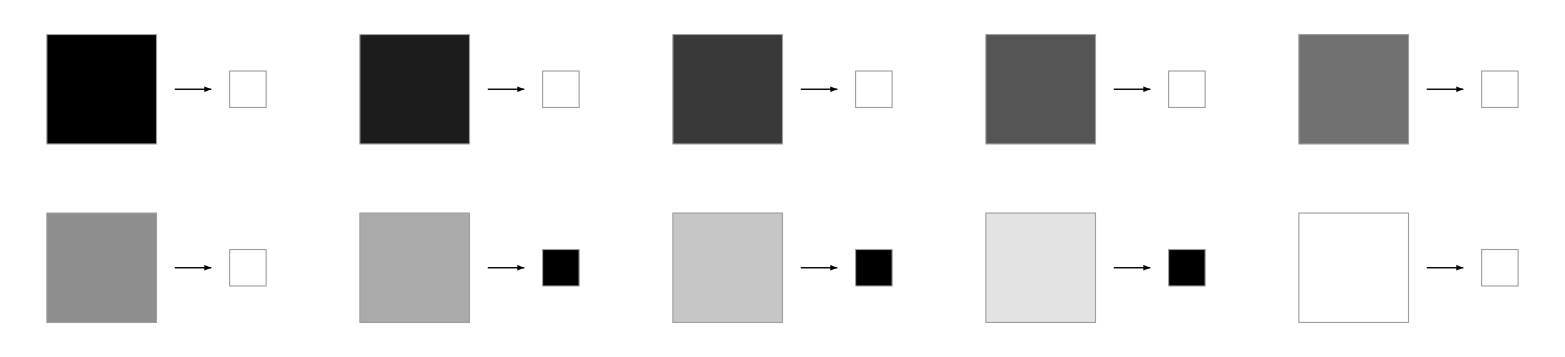

```mathematica
RulePlot[CellularAutomaton[{14, {2, 1}, {1, 1}}]]
```

```mathematica
CellularAutomaton[{14, {2, 1}, {1, 1}},{{{1}},0},{{{1}}}]
```

{{1,1,1},{1,1,1},{1,1,1}}

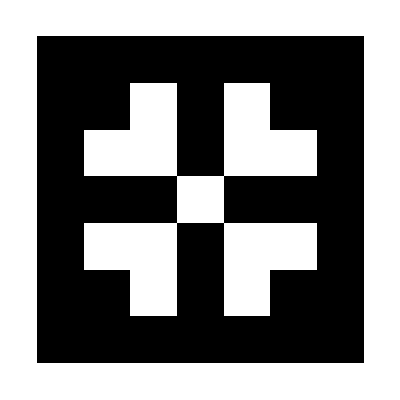

```mathematica
ArrayPlot[CellularAutomaton[{14, {2, 1}, {1, 1}},{{{1}},0},{{{3}}}]]
```

```mathematica
ArrayPlot[CellularAutomaton[{110,{2,{{0,2,0},{2,1,2},{0,2,0}}},{1,1}},{SparseArray[{{1,1},{1,100}}->1],0},{{{100}}}]]
```

-Graphics-

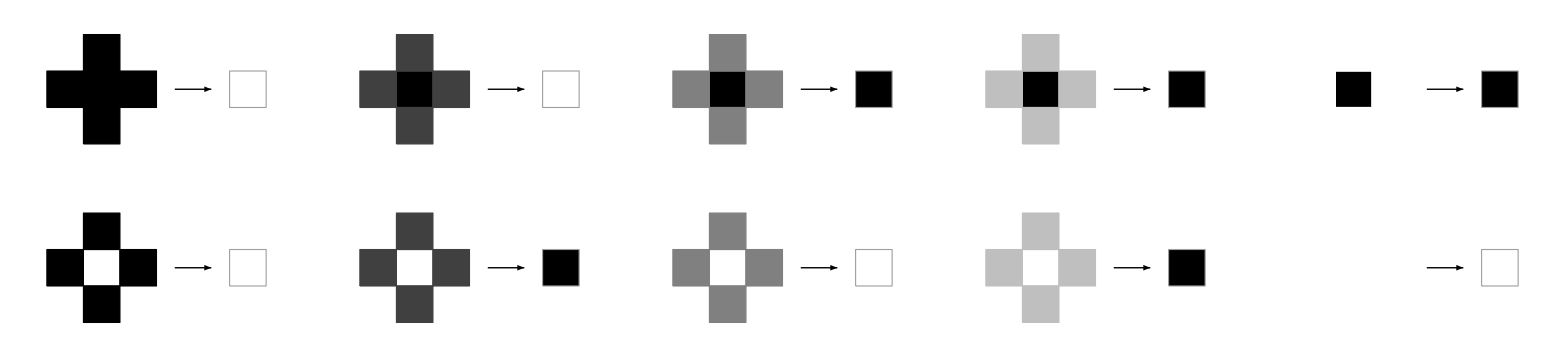

```mathematica
RulePlot[CellularAutomaton[{110,{2,{{0,2,0},{2,1,2},{0,2,0}}},{1,1}}]]
```

```mathematica
RulePlot[CellularAutomaton[<|"TotalisticCode"->14,"Dimension"->2|>]]
```

-Graphics-

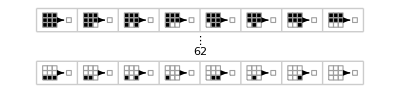

```mathematica
RulePlot[CellularAutomaton[{1024,2,{1,1}}]]
```

```mathematica
RulePlot[CellularAutomaton[{1024,{2,{2,1,2}},1}]]
```

RulePlot[CellularAutomaton[{1024,{2,{2,1,2}},1}]]

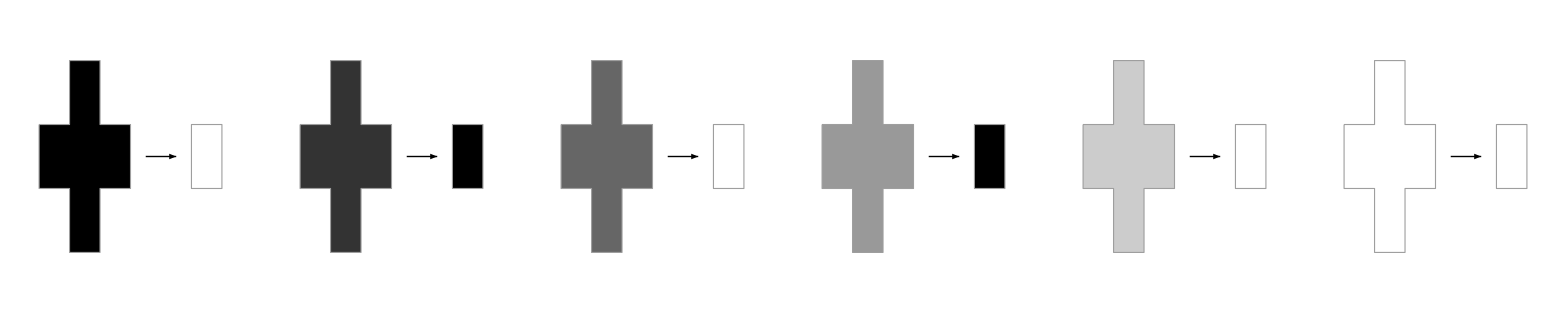

```mathematica
RulePlot[CellularAutomaton[{20,{2,{{0,1,0},{1,1,1},{0,1,0}}},{1,1}}]]
```

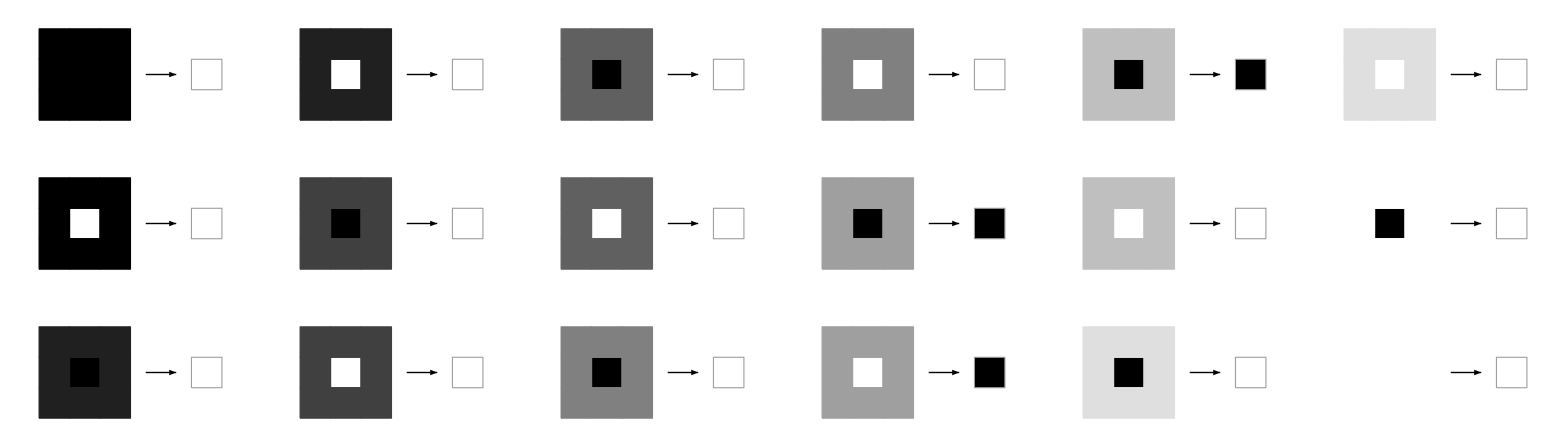

```mathematica
RulePlot[CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>],Appearance->"Simplified"]
```

```mathematica
2^10
```

1024

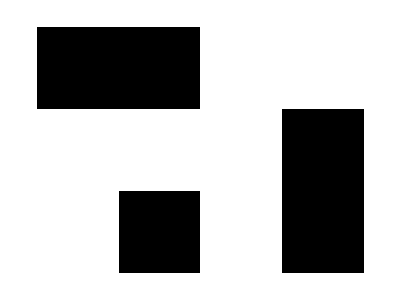

```mathematica
ArrayPlot[RandomInteger[1,{3,4}]]
```

```mathematica
ArrayPlot[SparseArray[{{1,1},{1,100}}->1]]
```

-Graphics-

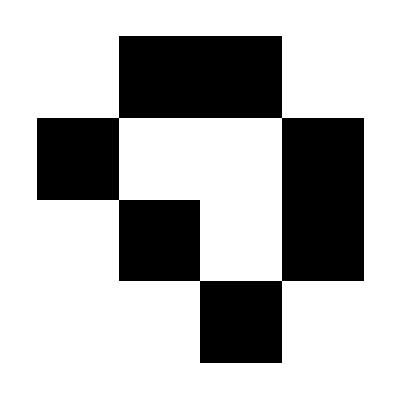

```mathematica
ArrayPlot[CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{RandomInteger[1,{6,6}],0},{{{80}}}]]
```

```mathematica
NetTrain
```

```mathematica
FeatureExtraction
```

```mathematica
dr=DimensionReduction[{-Graphics-,-Graphics-,-Graphics- ,-Graphics-,-Graphics-,-Graphics-},2]
```

DimensionReducerFunction[…]

```mathematica
dr[{-Graphics-,-Graphics-,-Graphics- ,-Graphics-,-Graphics-,-Graphics-}]
```

{{16.6901,0.663874},{8.66664,12.1655},{23.1908,-8.5953},{-14.2674,-21.1948},{-19.8211,-4.78483},{-14.459,21.7455}}

```mathematica
iris=ExampleData[{"MachineLearning","FisherIris"}, "Data"];
```

```mathematica
diris=DimensionReduction[iris[[All,1]],2, Method->"TSNE"]
```

DimensionReducerFunction[…]

```mathematica
byspecies=GroupBy[iris,Last->First];
```

```mathematica
byspecies=diris/@byspecies;
```

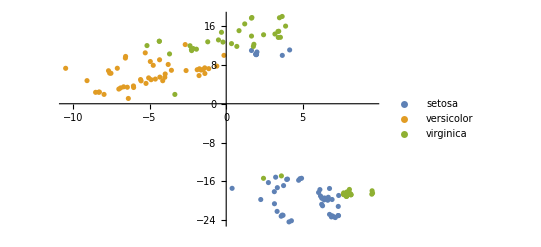

```mathematica
ListPlot[Values[byspecies], PlotLegends->Keys[byspecies]]
```

```mathematica
ListPlot[Values[byspecies], PlotLegends->Keys[byspecies]]
```

## AI for Conways Game of life

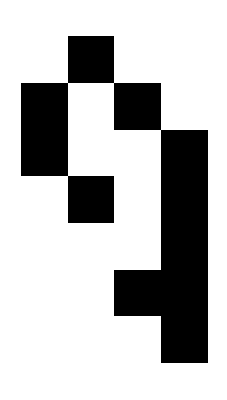

```mathematica
ArrayPlot[CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{RandomInteger[1,{6,6}],0},{{{1}}}]]
```

```mathematica
ArrayPlot[#]&/@CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{RandomInteger[1,{6,6}],0},{{800,804}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Get the set of array plots we want to analyze:

```mathematica
data=ArrayPlot[CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{RandomInteger[1,{6,6}],0},{{80,84}}]]&/@Range[1,100];
```

```mathematica
data//Dimensions
```

{100}

```mathematica
FeatureSpacePlot[data]
```

-Graphics-

```mathematica
Scaled[{{0,0,0},{0,1,1},{0,0,1}},2]
```

Scaled[{{0,0,0},{0,1,1},{0,0,1}},2]

```mathematica
start = RandomInteger[1,{4,4}];
data =ArrayPlot[#,Frame->False,ColorRules->{1->White,0->Black}]&/@CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{start,0},{{400,403}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
start=RandomInteger[1,{8,8}];
predata = CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{start,0},{{400,405}}];
morph=MorphologicalComponents[predata];
morph//Colorize
 comp = ComponentMeasurements[morph, "Count",All,"PropertyAssociation"];
maxpos = Max[comp["Count"]];,{i,1,10}]
```

-Graphics3D-

<|Count→{18,18,48,24,24,24,18,24,24,48,24,18,18}|>

```mathematica
ComponentMeasurements[morph,{"ConvexArea", "Count"},All,"PropertyAssociation"]
```

ComponentMeasurements::notsup: {ConvexArea} properties are not supported yet for Image3D and 3D arrays.

<|Count→{18,18,48,24,24,24,18,24,24,48,24,18,18}|>

```mathematica
comp["Count"]
```

{18,18,48,24,24,24,18,24,24,48,24,18,18}

```mathematica
Ordering[comp["Count"],-1]
```

{10}

```mathematica
ComponentMeasurements[morph, {"Count","LabelCount","Complexity"},All,"PropertyAssociation"]
```

<|Count→{30,30,30,30,155,36,23,128,24,2,24,109,2,123,30,18,18,42,36,36,24,24,36,30},LabelCount→{24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24},Complexity→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}|>

```mathematica
start={{0,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,0,0}}
predata = CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{start,0},{{400,405}}];
data =ArrayPlot[#,Frame->False,ColorRules->{1->White,0->Black}]&/@predata
```

{{0,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,0,0}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MorphologicalComponents[predata]//Colorize
```

-Graphics3D-

```mathematica
MorphologicalComponents[data[[1]],.1,Method->"BoundingBox"]//Colorize
```

-Graphics-

```mathematica
i=ArrayPlot[CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{start,0},{{{200}}}],Frame->False,ColorRules->{1->White,0->Black}]
```

-Graphics-

```mathematica
start={{0,1,1,1},{1,1,0,0},{1,1,0,1},{1,1,0,0}};
i=ArrayPlot[CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{start,0},{{{200}}}],Frame->False,ColorRules->{1->White,0->Black}]
```

-Graphics-

```mathematica
ImageMultiply[i,Dilation[i,2]]
```

-Graphics-

```mathematica
start1={{0,1,1,1},{1,1,0,0},{1,1,0,1},{1,1,0,0}};
ca1=CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{start1,0},{{{200}}}];
i1=ArrayPlot[ca1,Frame->False,ColorRules->{1->White,0->Black}];
```

```mathematica
clusters1=FindClusters[MeshPrimitives[ArrayMesh[ca1],2],DistanceFunction->(ChessboardDistance[RegionCentroid@#,RegionCentroid@#2]&)];
```

```mathematica
clusters1
```

```mathematica
Show[i1,Graphics@MapIndexed[{FaceForm[],EdgeForm[{Dotted,Cyan}],Scale[BoundingRegion[Join@@(PolygonCoordinates/@#),"FastEllipse"],{1,1} 1.1],EdgeForm[],Opacity[1],FaceForm[ColorData[97]@#2[[1]]],#}&,clusters1]]
```

-Graphics-

```mathematica
Dilation[i,1]
```

-Graphics-

```mathematica
ComponentMeasurements[i,"Shape"]
```

{1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-,5→-Graphics-,6→-Graphics-,7→-Graphics-,8→-Graphics-,9→-Graphics-,10→-Graphics-,11→-Graphics-,12→-Graphics-,13→-Graphics-}

```mathematica
start={{0,1,1,1},{1,1,0,0},{1,1,0,1},{1,1,0,0},{1,1,1,1}};
i=ArrayPlot[CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{start,0},{{{400}}}],Frame->False,ColorRules->{1->White,0->Black}]
```

-Graphics-

```mathematica
neighbourhood=1;
AbsoluteTiming[
dilated=Dilation[i,neighbourhood];
mask=Erosion[MorphologicalComponents[dilated],neighbourhood];
trimmed=ComponentMeasurements[{i,mask},"Image","PropertyAssociation"]["Image"];]
```

{0.0219235,Null}

```mathematica
mask//Colorize
```

-Graphics-

```mathematica
subimages
```

{1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-,5→-Graphics-,6→-Graphics-,7→-Graphics-,8→-Graphics-,9→-Graphics-,10→-Graphics-}

{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0},{0,0,1,0,1,1,0,0,0,0,1,1,0,0,0,1,1,0,1,1,0,1},{0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1},{0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,1,1,0,1,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0}}

```mathematica
dilated=Dilation[i,0]
```

{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0},{0,0,1,0,1,1,0,0,0,0,1,1,0,0,0,1,1,0,1,1,0,1},{0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1},{0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,1,1,0,1,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0}}

```mathematica
start={{0,1,1,1},{1,1,0,0},{1,1,0,1},{1,1,0,0},{1,1,1,1}};
i=CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{start,0},{{{100}}}];
dilated=Dilation[i,1];
morph=Erosion[MorphologicalComponents@dilated,1];
subimages=ComponentMeasurements[{i,morph},"Count"];
1/.subimages
```

109

```mathematica
ImagePadding
```

```mathematica
Trim[i,morph]
```

Trim[{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0},{0,0,1,0,1,1,0,0,0,0,1,1,0,0,0,1,1,0,1,1,0,1},{0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1},{0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,1,1,0,1,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0}},{{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,2,2,0,0,0,0,0,0,0,0,2,2},{0,0,1,1,1,1,0,0,0,0,2,2,0,0,0,2,2,2,2,2,2,2},{0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2},{0,0,0,1,1,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,2},{0,0,0,1,1,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,2},{0,0,0,1,1,0,0,0,0,0,0,0,0,2,2,2,2,2,2,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,2,2,2,2,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0}}]

```mathematica
morph//Colorize
```

-Graphics-

```mathematica
ComponentMeasurements[{i,morph},]
```

{1→0.0164677,2→0.0277325}

```mathematica
subimages
```

{1→109,2→51}

```mathematica
subimages//Values
```

{109,51}

```mathematica
subimages
```

{1→179}

```mathematica
start={{0,1,1,1},{1,1,0,0},{1,1,0,1},{1,1,0,0},{1,1,1,1}};
i=ArrayPlot[CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{start,0},{{{400}}}],Frame->False,ColorRules->{1->White,0->Black}];

dilated=Dilation[i,DiskMatrix[1]];
mask=Erosion[MorphologicalComponents@dilated,1];
subimages=ComponentMeasurements[{i,mask},"Image"];
4/.subimages
```

-Graphics-

```mathematica
start={{0,1,1,1},{1,1,0,0},{1,1,0,1},{1,1,0,0},{1,1,1,1}};
i=ArrayPlot[CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{start,0},{{{400}}}],Frame->False,ColorRules->{1->White,0->Black}];

dilated=Dilation[i,DiskMatrix[1]];
mask=Erosion[MorphologicalComponents@dilated,1];
subimages=ComponentMeasurements[{i,mask},"Image"];
4/.subimages
```

-Graphics-

```mathematica
mask//Colorize
```

-Graphics-

```mathematica
mask//Colorize
```

-Graphics-

```mathematica
MorphologicalComponents[dilated]//Colorize
```

-Graphics-

```mathematica
AbsoluteTiming[
dilated=Dilation[i,10];
mask=MorphologicalComponents@dilated;
trimmed=ComponentMeasurements[{i,mask},"Image"];]
```

{0.00708987,Null}

```mathematica
trimmed
```

{1→-Graphics-,2→-Graphics-}

```mathematica
AbsoluteTiming[
trim=Values@ComponentMeasurements[MorphologicalTransform[Binarize@i,"Max"],"BoundingBox"];
trimmed=ImageTrim[i,trim];]
```

{0.0326832,Null}

```mathematica
trimmed
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
trimmed
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
subimages = ComponentMeasurements[i, {"Image","Complexity"},All,"PropertyAssociation",CornerNeighbors->True]
```

<|Image→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Complexity→{0,0,0,0,0,0,0,0,0,1,1,0,0}|>

## Systematic Study

```mathematica
myarrayplot=ArrayPlot[#,ColorRules->{1->White,0->Black}]&
```

ArrayPlot[#1,ColorRules→{1→White,0→Black}]&

```mathematica
EvolveLargestCluster[start_,neighbourhood_,parts_,length_]:=Module[{},
i0=start;
Table[
If[Length[i0//Dimensions]==3,i0={{1,1},{1,1}};];
i=ArrayPlot[CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{i0,0},{{{IntegerPart[length/parts]}}}],Frame->False,ColorRules->{1->White,0->Black}];
If[First@i=={},Return[{}]];
dilated=Dilation[i,neighbourhood];
mask=MorphologicalComponents@dilated;
subimages=ComponentMeasurements[{i,mask},{"Image","Count"},"PropertyAssociation"];
maxindex=First@Ordering[subimages["Count"],-1];
i0= Round[ImageData[subimages["Image"][[maxindex]]]];

,{j,1,parts}];
ArrayPlot[i0,Frame->False,ColorRules->{1->White,0->Black}]
];
```

```mathematica
subimages["Image"]
```

{-Graphics-}

```mathematica
Dimensions[{{{1,1,1}},{{1,1,1}},{{1,1,1}}}]
```

{3,1,3}

```mathematica
i0
```

{{0,0,1,1,1,0,0},{0,0,0,0,0,0,0},{1,0,0,0,0,0,1},{1,0,0,0,0,0,1},{1,0,0,0,0,0,1},{0,0,0,0,0,0,0},{0,0,1,1,1,0,0}}

```mathematica
Binarize[-Graphics-]
```

-Graphics-

```mathematica
subimages
```

<|Image→{-Graphics-},Count→{4}|>

```mathematica
EvolveLargestCluster[RandomInteger[1,{30,30}],4,4,2000]
```

-Graphics-

```mathematica
data={};
Monitor[
Table[
	start=RandomInteger[1,{8,8}];
	largestcomp = EvolveLargestCluster[start,4,3,2000];
	
	comp = ComponentMeasurements[largestcomp, "Count",All,"PropertyAssociation"];
	max = Max[comp["Count"]];
	If[max>8,AppendTo[data,{start,max}];];
,{jj,1,1000}],jj];
data
```

```mathematica
myarrayplot[data[[1,1]]]
```

-Graphics-

```mathematica
EvolveLargestCluster[data[[1,1]],10,1,15]
```

-Graphics-

```mathematica
E
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

{}

```mathematica
data={};

Table[
	start=RandomInteger[1,{8,8}];
	predata = CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{start,0},{{4000,4008}}];
	If[predata[[1]]≠ {},
	morph=MorphologicalComponents[predata];
	comp = ComponentMeasurements[morph, "Count",All,"PropertyAssociation"];
	max = Max[comp["Count"]];
	If[max>8*8,AppendTo[data,{start,max}];];
	];
,{i,1,100}]
data
```

```mathematica
If[predata[[1]]=={},Print["y"],Print["n"]]
```

y

```mathematica
MorphologicalComponents[predata]
```

MorphologicalComponents::imginv: Expecting an image or graphics instead of {{},{},{},{},{},{}}.

MorphologicalComponents[{{},{},{},{},{},{}}]

```mathematica
morph=MorphologicalComponents[predata];
morph//Colorize
```

```mathematica
predata[[1]]//ArrayPlot
```

-Graphics-

```mathematica
predata = CellularAutomaton[<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->9|>,{data[[2,1]],0},{{4000,4008}}];
morph=MorphologicalComponents[predata];
morph//Colorize
```

-Graphics3D-